Means; initial conditions are that at t=0 there is, on average, one A cell, and one B cell:

```mathematica
DSolve[{n'[t] == λ - γ n[t], n[0]==1},n,t]
DSolve[{l'[t] == γ n[t], l[0]==0}, l, t]
```

{{n→Function[{t},(ⅇ^(-t γ) (γ-λ+ⅇ^(t γ) λ))/γ]}}

{{l→Function[{t},-∫_1^0 γ n[K[1]]ⅆK[1]+∫_1^t γ n[K[1]]ⅆK[1]]}}

```mathematica
nA[t_]:=1
nB[t_]:=(1-λ/γ) Exp[-γ t]+λ/γ
nC[t_]:=Evaluate[Integrate[γ nB[τ],{τ,0,t}]]
```

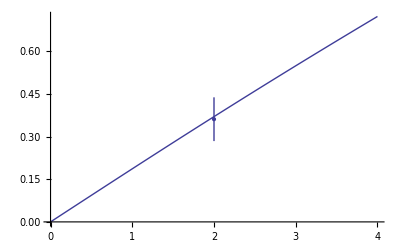

```mathematica
plfit = Plot[nC[t]/(nA[t]+nB[t])//.{λ->1/4,γ->(λ ρ)/(1-ρ),ρ->0.6},{t,0,4}];
Needs["ErrorBarPlots`"]
pldata = ErrorListPlot[{{2,30/83},ErrorBar[30/83 * Sqrt[1/30+1/83]]}];
Show[plfit, pldata]
```

Initial conditions

```mathematica
P0[2,0,0]:=r
P0[1,1,0]:=1-2 r
P0[0,2,0]:=r
P0[m_,n_,l_]:=0
```

Coupled differential equations

```mathematica
P[m_,n_,l_,t_]:=If[m<0||n<0||l<0,0,Exp[-(λ m+n γ) t] (P0[m,n,l]+∫_0^t Exp[(λ m+n γ) τ] (λ (r (m-1) P[m-1,n,l,τ]+r (m+1) P[m+1,n-2,l,τ]+(1-2 r) m P[m,n-1,l,τ])+γ (n+1) P[m,n+1,l-1,τ])ⅆτ)]
```

Combine basal cells

```mathematica
Pmn[mn_,l_,t_]:= Sum[P[m,mn-m,l,t],{m,0,mn}]
```

```mathematica
P[0,0,2,t]
P[0,1,1,t]
```

ⅇ^(-2 t γ) (-1+ⅇ^(t γ))^2 r

2 ⅇ^(-t γ) (1-ⅇ^(-t γ)) r

```mathematica
PDX[{{b_,s_},n_}] := Pmn[b,s,t]^n
PDXT[{b_,s_}] := Tooltip[Pmn[b,s,t], {b,s}]
```

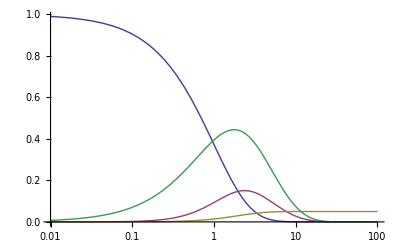

```mathematica
LogLinearPlot[Evaluate[PDXT/@{{2,0},{2,1}, {0,2}, {1,1}} /. {λ->1/4, γ->3/4, r->0.05}], {t,0.01,100}]
```

```mathematica
Prior=PDF[UniformDistribution[{1/10,9/10}],ρ]PDF[UniformDistribution[{1/100,1/2}],r];
```

```mathematica
TotalPDX=Times@@PDX/@{{{1,1},6},{{2,0},12},{{0,2},2},{{2,1},20},{{3,0},4},{{4,0},1}}//.{γ->(λ ρ)/(1-ρ),t->2,λ->1/4};
```

```mathematica
{Z,Subscript[ρ, 0],Subscript[r, 0]}=NIntegrate[{1,ρ,r} * TotalPDX * Prior,{ρ,0.1,0.9},{r,0.01,0.5}];
{Subscript[ρ, 0],Subscript[r, 0]} / Z
```

{0.579713,0.0973389}

```mathematica
FindMaximum[TotalPDX / Z * Prior, {ρ,0.1,0.9}, {r,0.01,0.5}]
```

{70.3184,{ρ→0.582518,r→0.0709927}}

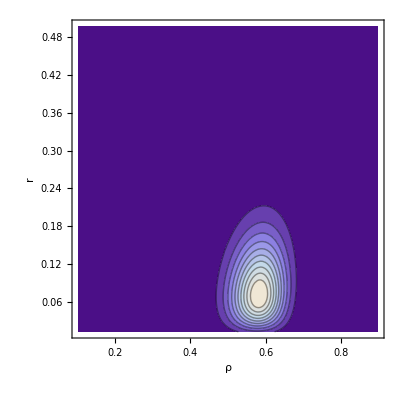

```mathematica
ContourPlot[TotalPDX / Z * Prior,{ρ,0.1,0.9}, {r,0.01,0.5},Contours->10,FrameLabel->{ρ,r}, PlotRange->All]
```